# BTC-USD Moving Averages

```mathematica
Clear["Global`*"]
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
SetDirectory[NotebookDirectory[]];
settings=<|
aspectratio->1/3
,imagemargins->20
,imagesize->1200
,labelstyle->{16}
,origindate->"Jul. 1, 2017"
,plotbackground->Lighter[LightGray,0.75]
,subtitlestyle -> {15}
,ticksstyle->{18}
,titlestyle->{20,Red}
|>;
(* Function shortcuts *)
(*st=StringTemplate;*)
dollar[a_]:=StringTemplate["$``"][NumberForm[a,DigitBlock->3]];
updatedstr=Style[StringTemplate["(updated: ``)"][DateString[]],settings[subtitlestyle]];

btcData=FinancialData[
"BTC/USD"
,settings[origindate]
];
mo100=MovingAverage[btcData,100];
mo100latest=dollar[mo100["LastValue"]];
mo200=MovingAverage[btcData,200];
mo200latest=dollar[mo200["LastValue"]];
mo1yr=MovingAverage[btcData,365];
mo1yrlatest=dollar[mo1yr["LastValue"]];
mo2yr=MovingAverage[btcData,365*2];
mo2yrlatest=dollar[mo2yr["LastValue"]];
mo3yr=MovingAverage[btcData,365*3];
mo3yrlatest=dollar[mo3yr["LastValue"]];
mo4yr=MovingAverage[btcData,365*4];
mo4yrlatest=dollar[mo4yr["LastValue"]];
mo5yr=MovingAverage[btcData,365*5];
mo5yrlatest=dollar[mo5yr["LastValue"]];

plottypefunc=DateListPlot;
lines=Range[1];
selectlines=CheckboxBar[
Dynamic[lines]
,Map[Style[#,{16}]&,({1->"BTC",2->"100 day",3->"200 day",4->"1 year",5->"2 year", 6-> "3 year", 7-> "4 year", 8-> "5 year"}//Association)]//Normal
,Method->"Active"
];
plottype=1;
selectplottype=RadioButtonBar[
Dynamic[plottype]
,Map[Style[#,16]&,({1->"Linear",2->"Log"}//Association)]//Normal
,Method->"Active"
];
plotlines={
btcData
,mo100
,mo200
, mo1yr
, mo2yr
, mo3yr
, mo4yr
, mo5yr
};
plotlabels={"BTC"
,StringTemplate["100 Day MA: ``"][mo100latest]
,StringTemplate["200 Day MA: ``"][mo200latest]
,StringTemplate["1 Yr MA: ``"][mo1yrlatest]
,StringTemplate["2 Yr MA: ``"][mo2yrlatest]
,StringTemplate["3 Yr MA: ``"][mo3yrlatest]
,StringTemplate["4 Yr MA: ``"][mo4yrlatest]
,StringTemplate["5 Yr MA: ``"][mo5yrlatest]
};
plotlegends={"BTC (USD)"
,"100 Day MA"
,"200 Day MA"
,"1 Year MA"
,"2 Year MA"
,"3 Year MA"
,"4 Year MA"
,"5 Year MA"
};
```

```mathematica
Manipulate[
Module[
{detail,filename, maplot,plotlabel, plottypefunc}
,plotlabel=Column[
Join[{
Style["Bitcoin Price (USD)" ,settings[titlestyle]]
,Style["Latest: $"  <> ToString[NumberForm[btcData["LastValue"],DigitBlock->3]],settings[subtitlestyle]]
}
,Style[#,settings[subtitlestyle]]&/@Part[
plotlabels
,Select[lines,#!=1&]
]
]
,Center
];
plottypefunc:=If[plottype==1,DateListPlot,DateListLogPlot];
maplot=plottypefunc[
Part[
plotlines
,lines
]
,Background->settings[plotbackground]
,FrameTicks->All
,GridLines->{
Join[DateRange[{2010},{2030},Quantity[1,"Months"]],{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]]
,Range[0,200000,10000]
}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,TicksStyle->settings[ticksstyle]
,PlotLabel->Column[
{
plotlabel
,updatedstr
}
,Center]
,PlotLegends->Placed[
SwatchLegend[Part[
plotlegends
,lines
],LegendFunction->(Framed[#,Background->settings[plotbackground]]&)]
,{Left,Top}
]
];
If[
plottype==1 
&& Length[lines]==2
&& First[lines]==1
,(
detail =StringReplace[
Last[
Part[
plotlegends
,lines
]
]
," "-> "-"
];
filename = "BTC-USD-"<>detail<>".jpg";
Export[filename,maplot];
)
];
maplot
]
,Dynamic[selectlines]
,Dynamic[selectplottype]
]
```

## Past n days moving average

```mathematica
Manipulate[
Module[
{btcn, mon, meann,mean}
,btcn=Take[btcData//Normal,-n];
mon= Take[MovingAverage[btcData,n]//Normal,-n];
(*mon= MovingAverage[btcData,n]//Normal;*)
mean=Mean[Last /@btcn];
meann=NumberForm[Mean[Last /@btcn],DigitBlock->3];
plotlabel = Column[{
Style["Bitcoin Price (USD)" ,settings[titlestyle]]
,Style["Latest: $"  <> ToString[NumberForm[btcData["LastValue"],DigitBlock->3]] ,settings[subtitlestyle]]
,Style["Current " <> ToString[n]<>" Day Moving Average: "<>dollar[meann],settings[subtitlestyle]]
,updatedstr
}
,Center
];
Column[{
DateListPlot[
{btcn, mon}
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,FrameTicks->All
,GridLines->{
Join[DateRange[{2010},{2030},Quantity[1,"Months"]],{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]]
,Join[{{mean,Directive[{Red,Thick, Dashed}]}},Range[0,200000,5000]]
}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,LabelStyle->settings[labelstyle]
,PlotLabel->plotlabel
,PlotLegends->{
"Price"
,ToString[n] <> " Day Moving Average"
}
,PlotRange->Full
,TicksStyle->settings[ticksstyle]
]
,Spacer[20]
,DateListPlot[
{First[#]//First,N[((First[#]//Last)-(Last[#]//Last))/(Last[#]//Last)]}&/@ MapThread[List,{btcn,mon}]
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,FrameTicks->{All,{#,PercentForm[#]}&/@Join[Range[-5,-0.1,0.1],{0},Range[0.1,5,0.1]]}
,GridLines->{
Join[DateRange[{2010},{2030},Quantity[1,"Months"]],{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]]
, Join[Range[-10,10,0.05],{{0,Thick}}]
}
,LabelStyle->settings[labelstyle]
,TicksStyle->settings[ticksstyle]
,PlotLabel->Column[{
Style["Relative above/below the moving average",settings[titlestyle]]
,updatedstr
}
,Center
]

]
}]
]
,{{n,200,Style["Moving Average",16]},Join[{100-> "100 days",200 -> "200 days",500-> "500 days"},MapIndexed[#1 -> ToString[First[#2]] <> " yr"&,Range[365,365 * 6,365]]]//Sort}
]
```

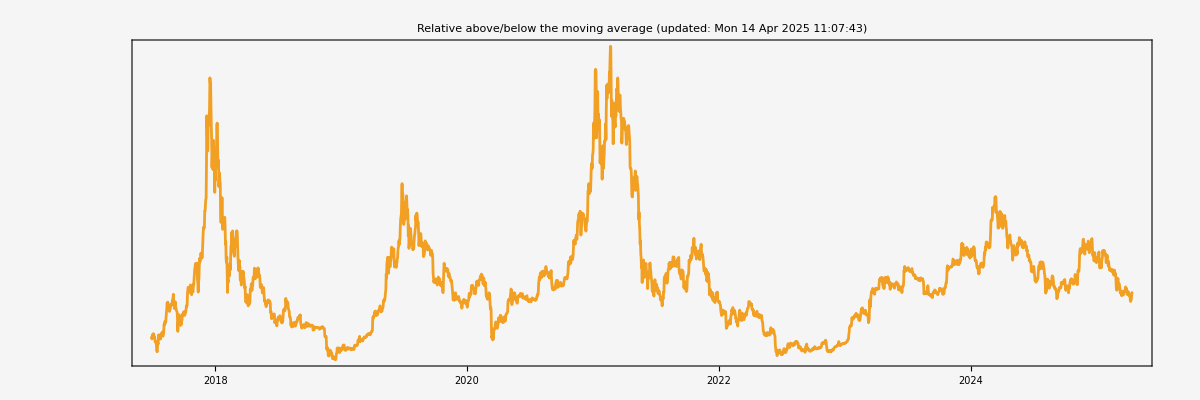

```mathematica
int1=TimeSeriesThread[(#[[1]]-#[[2]])/(#[[2]])&,{plotlines[[1]],plotlines[[4]]},ResamplingMethod->{"Interpolation",InterpolationOrder->1}];
(* see: https://community.wolfram.com/groups/-/m/t/377031 *)
DateListPlot[
{{},int1}/. {}->{{{},}}
,AspectRatio->settings[aspectratio]
,Background->settings[plotbackground]
,FrameTicks->{All,{#,PercentForm[#]}&/@Join[Range[-50,-0.25,0.25],{0},Range[0.25,50,0.25]]}
,GridLines->{
Join[
DateRange[{2010},{2030},Quantity[1,"Months"]]
,{#,Thick}&/@DateRange[{2010},{2030},Quantity[1,"Years"]]
]
,Join[Range[-10,10,0.1]
,{#,Thick}&/@Range[-10,10]
]
}
,ImageMargins->settings[imagemargins]
,ImageSize->settings[imagesize]
,LabelStyle->settings[labelstyle]
,PlotLabel->Column[{
Style["Relative above/below the moving average",settings[titlestyle]]
,updatedstr
}
,Center
]
,PlotRange->Full
,TicksStyle->settings[ticksstyle]
]
```

```mathematica
Table[plotlines[[x]],{x,1,8}]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}